```mathematica
f11={{1,0,0},{0,1,0},{0,0,1}};
f22={{1,0,0},{0,-1,0},{0,0,0}};
f33=1/Sqrt[3] {{1,0,0},{0,1,0},{0,0,-2}};
f12={{0,1,0},{1,0,0},{0,0,0}};
f21={{0,-I,0},{I,0,0},{0,0,0}};
f13={{0,0,1},{0,0,0},{1,0,0}};
f31={{0,0,-I},{0,0,0},{I,0,0}};
f23={{0,0,0},{0,0,1},{0,1,0}};
f32={{0,0,0},{0,0,-I},{0,I,0}};

u={{1,0,0},{0,-1,0},{0,0,-1}};

Id=IdentityMatrix[3];
Hint= 1/2(KroneckerProduct[f12,f12,Id,Id]+KroneckerProduct[f21,f21,Id,Id]+KroneckerProduct[f13,f13,Id,Id]+KroneckerProduct[f31,f31,Id,Id]+KroneckerProduct[Id,f12,f12,Id]+KroneckerProduct[Id,f21,f21,Id]+KroneckerProduct[Id,f13,f13,Id]+KroneckerProduct[Id,f31,f31,Id]+KroneckerProduct[Id,Id,f12,f12]+KroneckerProduct[Id,Id,f21,f21]+KroneckerProduct[Id,Id,f13,f13]+KroneckerProduct[Id,Id,f31,f31]);

Hid=1/2((√3)/2(KroneckerProduct[f12,f12,Id,Id]+KroneckerProduct[f21,f21,Id,Id]+KroneckerProduct[f13,f13,Id,Id]+KroneckerProduct[f31,f31,Id,Id])+1(KroneckerProduct[Id,f12,f12,Id]+KroneckerProduct[Id,f21,f21,Id]+KroneckerProduct[Id,f13,f13,Id]+KroneckerProduct[Id,f31,f31,Id])+(√3)/2(KroneckerProduct[Id,Id,f12,f12]+KroneckerProduct[Id,Id,f21,f21]+KroneckerProduct[Id,Id,f13,f13]+KroneckerProduct[Id,Id,f31,f31]));

η0=Flatten[KroneckerProduct[{0,1,0},{1,0,0},{1,0,0},{1,0,0}]];
η1=Flatten[KroneckerProduct[{1,0,0},{1,0,0},{1,0,0},{0,1,0}]];

g0=KroneckerProduct[Id,Id,Id,Id];
g1=KroneckerProduct[u,Id,Id,u];

StateFidelity1[τ_]:=Abs[η1.MatrixExp[-I τ π Hid].η0]^2
StateFidelity2[τ_]:=Abs[η1.MatrixExp[-I τ π Hint].η0]^2
StateFidelity3[τ_,m_]:=Abs[η1.MatrixPower[MatrixExp[-I 14/(15 m) τ π Hint].g1†.MatrixExp[-I 1/(15 m)τ π Hint].g1,m].η0]^2
```

```mathematica
StateFidelityAll1=Plot[{StateFidelity1[t],StateFidelity2[t]},{t,0,8},
PlotStyle->{Darker@Green,Red},
AxesLabel->{"tπ","F(t)"}]

StateFidelityAll2=Plot[{StateFidelity3[t,1],StateFidelity3[t,16]},{t,0,8},
PlotStyle->{Orange,Blue},
AxesLabel->{"tπ","F(t)"}]
```

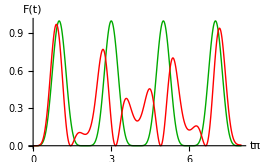
```mathematica
Export["StateFidelity1.pdf",-Graphics-];
```

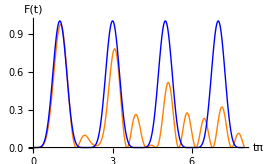
```mathematica
Export["StateFidelity2.pdf",-Graphics-];
```

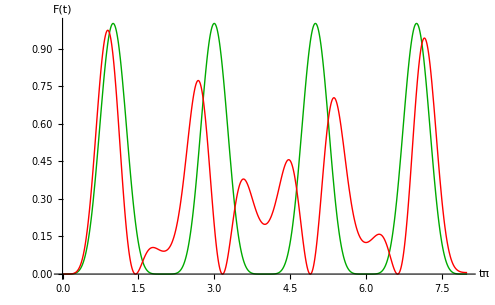
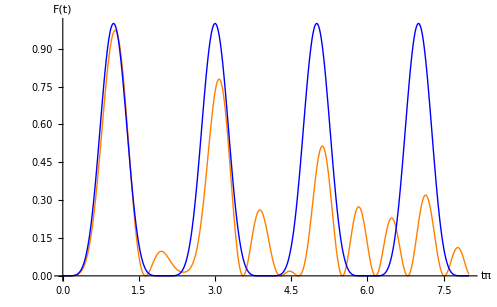
```mathematica
Export["StateFidelityAll.pdf",-Graphics--Graphics-];
```

```mathematica
EntanglementFidelity0[m_]:=N[Abs[1/3^4 Tr[MatrixPower[MatrixExp[I π Hid],m].MatrixPower[MatrixExp[-I π Hint],m]]]^2]
EntanglementFidelity1[m_,Δt_]:=N[Abs[1/3^4 Tr[MatrixPower[MatrixExp[I π Hid],m].MatrixPower[MatrixExp[-I 14/(15Δt) π Hint].g1†.MatrixExp[-I 1/(15Δt)π Hint].g1,m Δt]]]^2]
```

```mathematica
FidelityPlot1=
DiscretePlot[{EntanglementFidelity0[m],EntanglementFidelity1[m,1],EntanglementFidelity1[m,16]},{m,0,8},
AxesLabel->{"tπ","F(Δt,t)"},
PlotRange->{0,1},
PlotStyle->{Red,Darker@Green,Darker@Blue},
Filling->None,
Joined->True,
PlotMarkers->Tiny]
```

```mathematica
Export["FidelityPlot 4 Qutrits.pdf",FidelityPlot1];
```

```mathematica
F[m_]:=Abs[1/3^4 Tr[MatrixPower[N[MatrixExp[I 15 π/m Hid],100],m].MatrixPower[N[MatrixExp[-I 14 π/m Hint].g1†.MatrixExp[-I π/m Hint].g1,100],m]]]^2
```

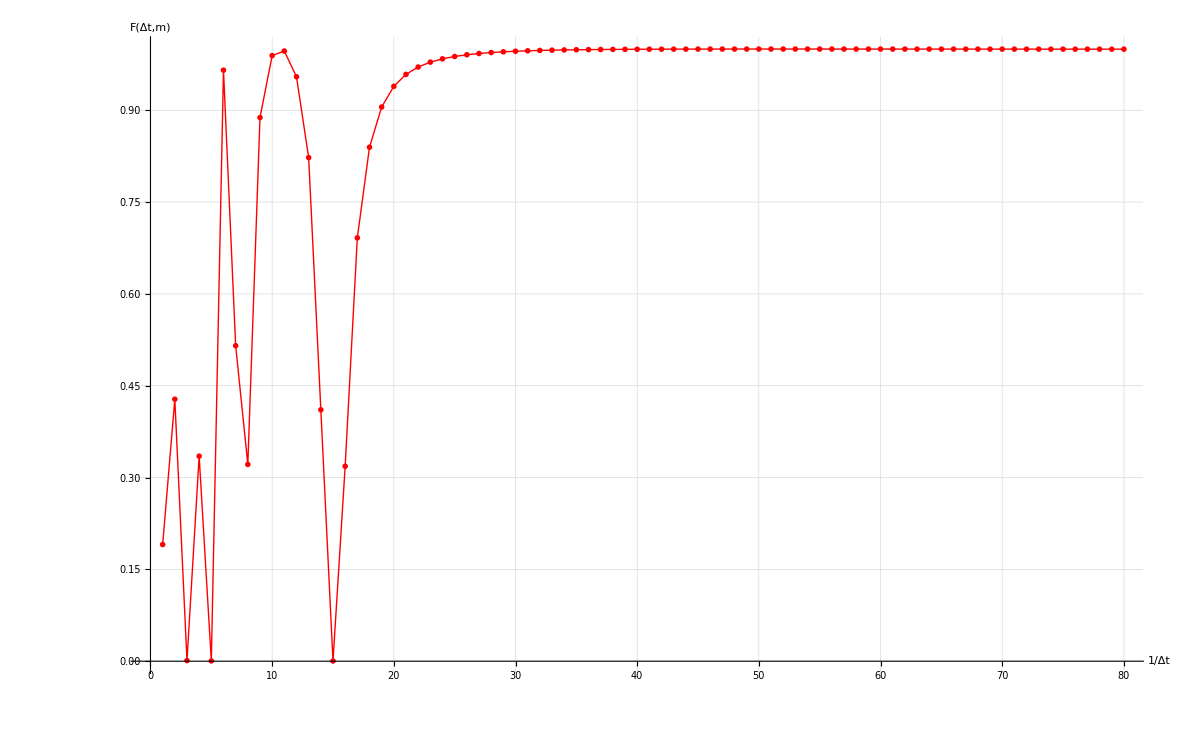

```mathematica
FidelityPlot3=
DiscretePlot[F[m],{m,1,80},
AxesLabel->{"1/Δt","F(Δt,m)"},
Joined->True,
Filling->None,
PlotRange-> {0,1},
PlotMarkers->{Automatic,Tiny},
PlotStyle->{Red,Darker@Green,Darker@Blue},
GridLines->Automatic]
```

```mathematica
Export["KonvergenzNeu.pdf",FidelityPlot3];
```